```mathematica
Clear["Global`*"]
```

Problem Set 1.5. 3--13. General Solution. Initial value problems.
Find the general solution. If an initial condition is given, find also the corresponding particular solution and graph or sketch it. (Show the details of your work.)

3. y' - y = 5.2

```mathematica
eqn = y'[x]-y[x] ==5.2;
sol = DSolve[eqn,y,x]
```

{{y→Function[{x},-5.2+ⅇ^(1. x) C[1]]}}

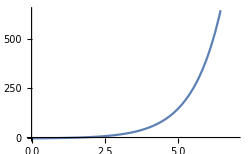

```mathematica
Plot[-5.2+ⅇ^(1. x),{x,0,7},ImageSize->250]
```

```mathematica
Clear["Global`*"]
```

4. y' = 2y - 4x

```mathematica
eqn = y'[x]==2 y[x]-4 x;
sol = DSolve[eqn, y,x]
```

{{y→Function[{x},-4 (-1/4-x/2)+ⅇ^(2 x) C[1]]}}

```mathematica
Simplify[eqn/.sol]
```

{True}

```mathematica
Clear["Global`*"]
```

5. y' + ky = ⅇ^-kx

```mathematica
eqn = y'[x]+k y[x]==Exp[-k x];
sol = DSolve[eqn,y,x]
```

{{y→Function[{x},ⅇ^(-k x) x+ⅇ^(-k x) C[1]]}}

```mathematica
eqn/.sol//Simplify
```

{True}

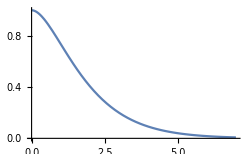

```mathematica
Plot[ⅇ^(-k x) x+ⅇ^(-k x)/.k->1 ,{x,0,7},ImageSize->250]
```

```mathematica
Clear["Global`*"]
```

6. y' + 2y = 4 cos 2x, y(1/4 π=3)

```mathematica
eqn = y'[x]+2 y[x]==4 Cos[2 x];
sol = DSolve[{eqn,y[π/4]==3},y,x]
```

{{y→Function[{x},ⅇ^(-2 x) (2 ⅇ^(π/2)+ⅇ^(2 x) Cos[2 x]+ⅇ^(2 x) Sin[2 x])]}}

```mathematica
eqn/.sol
```

{True}

```mathematica
y[π/4]/.sol[[1]]
```

3

```mathematica
Clear["Global`*"]
```

7. xy' = 2y + x^3 ⅇ^x

```mathematica
eqn = x y'[x]==2 y[x]+x^3 ⅇ^x;
sol = DSolve[eqn,y,x]
```

{{y→Function[{x},ⅇ^x x^2+x^2 C[1]]}}

```mathematica
eqn/.sol//Simplify
```

{True}

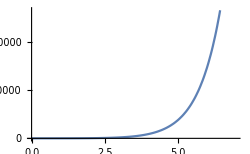

```mathematica
Plot[ⅇ^x x^2+x^2 ,{x,0,7},ImageSize->250]
```

```mathematica
Clear["Global`*"]
```

8. y' + y tan x = ⅇ^(-0.01x) cos x, y(0) = 0

```mathematica
eqn = y'[x]+y[x] Tan[x]==ⅇ^(-0.01 x) Cos[x];
sol = DSolve[{eqn,y[0]==0},y,x]
```

{{y→Function[{x},1/((ⅇ^(-ⅈ x)+ⅇ^(ⅈ x))^2.)(100.+1.07119×10^-16 ⅈ) ⅇ^((-0.01-2. ⅈ) x) ((1.+0. ⅈ) ⅇ^((0.01+2. ⅈ) x) (ⅇ^(-ⅈ x)+ⅇ^(ⅈ x))^2. Cos[x]^1.-(1.-2.73653×10^-18 ⅈ) (1.+ⅇ^(2 ⅈ x))^2. Cos[x]^1. Hypergeometric2F1[0.+0.005 ⅈ,2.,1.+0.005 ⅈ,-1. ⅇ^((0.+2. ⅈ) x)]-(0.0000499988+0.00999975 ⅈ) ⅇ^((0.+2. ⅈ) x) (1.+ⅇ^(2 ⅈ x))^2. Cos[x]^1. Hypergeometric2F1[1.+0.005 ⅈ,2.,2.+0.005 ⅈ,-1. ⅇ^((0.+2. ⅈ) x)]-(6.24996×10^-6+0.00249998 ⅈ) ⅇ^((0.+4. ⅈ) x) (1.+ⅇ^(2 ⅈ x))^2. Cos[x]^1. Hypergeometric2F1[2.,2.+0.005 ⅈ,3.+0.005 ⅈ,-1. ⅇ^((0.+2. ⅈ) x)])]}}

```mathematica
FullSimplify[eqn/.sol]
```

{1/Cos[x]^3. ⅇ^((-0.01-6. ⅈ) x) (1. ⅇ^((0.+6. ⅈ) x) Cos[x]^4.+(1.+ⅇ^(2 ⅈ x))^1. Cos[x]^2. ((5.55112×10^-17+100. ⅈ) ⅇ^((0.+6. ⅈ) x) Hypergeometric2F1[0.+0.005 ⅈ,2.,1.+0.005 ⅈ,-1. ⅇ^((0.+2. ⅈ) x)]-(0.999975-0.00499988 ⅈ) ⅇ^((0.+8. ⅈ) x) Hypergeometric2F1[1.+0.005 ⅈ,2.,2.+0.005 ⅈ,-1. ⅇ^((0.+2. ⅈ) x)]-(0.249998-0.000624996 ⅈ) ⅇ^((0.+10. ⅈ) x) Hypergeometric2F1[2.,2.+0.005 ⅈ,3.+0.005 ⅈ,-1. ⅇ^((0.+2. ⅈ) x)])+(1.38778×10^-17+25. ⅈ) (1.+ⅇ^(2 ⅈ x))^2. (((1. ⅇ^((0.+3. ⅈ) x)-1. ⅇ^((0.+5. ⅈ) x)) Cos[x]^1.-(2.-0.01 ⅈ) ⅇ^((0.+4. ⅈ) x) Cos[x]^2.) Hypergeometric2F1[0.+0.005 ⅈ,2.,1.+0.005 ⅈ,-1. ⅇ^((0.+2. ⅈ) x)]+((0.0000499988+0.00999975 ⅈ) (1. ⅇ^((0.+5. ⅈ) x)-1. ⅇ^((0.+7. ⅈ) x)) Cos[x]^1.-(0.0000999975-4.99988×10^-7 ⅈ) ⅇ^((0.+6. ⅈ) x) Cos[x]^2.) Hypergeometric2F1[1.+0.005 ⅈ,2.,2.+0.005 ⅈ,-1. ⅇ^((0.+2. ⅈ) x)]+((6.24996×10^-6+0.00249998 ⅈ) ⅇ^((0.+7. ⅈ) x)-(6.24996×10^-6+0.00249998 ⅈ) ⅇ^((0.+9. ⅈ) x)) Cos[x]^1. Hypergeometric2F1[2.,2.+0.005 ⅈ,3.+0.005 ⅈ,-1. ⅇ^((0.+2. ⅈ) x)]+Cos[x]^2. ((-0.0000999975-0.0199995 ⅈ) ⅇ^((0.+6. ⅈ) x) Hypergeometric2F1[1.+0.005 ⅈ,3.,2.+0.005 ⅈ,-1. ⅇ^((0.+2. ⅈ) x)]+ⅇ^((0.+8. ⅈ) x) ((-0.0000124999+0.00500003 ⅈ) Hypergeometric2F1[2.,2.+0.005 ⅈ,3.+0.005 ⅈ,-1. ⅇ^((0.+2. ⅈ) x)]-(0.0000499997+0.0199999 ⅈ) Hypergeometric2F1[2.+0.005 ⅈ,3.,3.+0.005 ⅈ,-1. ⅇ^((0.+2. ⅈ) x)])-(0.0000111111+0.00666665 ⅈ) ⅇ^((0.+10. ⅈ) x) Hypergeometric2F1[3.,3.+0.005 ⅈ,4.+0.005 ⅈ,-1. ⅇ^((0.+2. ⅈ) x)])))==0}

```mathematica
y[0]/.sol[[1]]
```

-3.99529×10^-15+1.73472×10^-16 ⅈ

This does not seem very satisfactory. The initial value is not even recoverable, apparently.

```mathematica
Clear["Global`*"]
```

9. y' + y sin x = ⅇ^(cos x), y(0) = -2.5

```mathematica
eqn = y'[x]+y[x] Sin[x]==ⅇ^Cos[x];
sol = DSolve[{eqn, y[0]==-2.5},y,x]
```

{{y→Function[{x},-0.919699 ⅇ^Cos[x]+ⅇ^Cos[x] x]}}

The particular solution is checked.

```mathematica
eqn/.sol//Simplify
```

{True}

```mathematica
y[0]/.sol[[1]]
```

-2.5

```mathematica
solg = DSolve[{eqn},y,x]
```

{{y→Function[{x},ⅇ^Cos[x] x+ⅇ^Cos[x] C[1]]}}

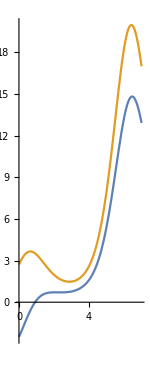

```mathematica
Plot[{-0.9196986029286058 ⅇ^Cos[x]+ⅇ^Cos[x] x ,ⅇ^Cos[x] x+ⅇ^Cos[x]},{x,0,7},ImageSize->150,AspectRatio->Automatic,GridLines->All]
```

```mathematica
Clear["Global`*"]
```

10. y' cos x + (3y - 1) sec x = 0, y(π/4) = 4/3

```mathematica
eqn = y'[x] Cos[x]+(3 y[x]-1) Sec[x]==0;
sol = DSolve[{eqn,y[π/4]==4/3},y,x]
```

{{y→Function[{x},1/3 ⅇ^(-3 Tan[x]) (3 ⅇ^3+ⅇ^(3 Tan[x]))]}}

```mathematica
eqn/.sol//Simplify
```

{True}

```mathematica
y[π/4]/.sol[[1]]
```

4/3

```mathematica
Clear["Global`*"]
```

11. y' = (y - 2) cot x

```mathematica
eqn = y'[x]==(y[x]-2) Cot[x];
sol = DSolve[eqn,y,x]
```

{{y→Function[{x},2+C[1] Sin[x]]}}

```mathematica
eqn/.sol
```

{True}

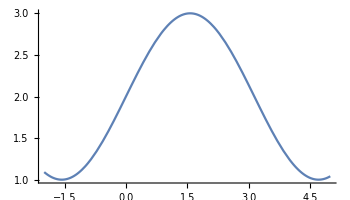

```mathematica
Plot[2+ Sin[x],{x,-2,5},ImageSize->350,AspectRatio->Automatic,GridLines->All]
```

```mathematica
Clear["Global`*"]
```

12. xy' + 4y = 8 x^4, y(1) = 2

```mathematica
eqn=x y'[x]+4 y[x]==8 x^4;
sol = DSolve[{eqn,y[1]==2},y,x]
```

{{y→Function[{x},(1+x^8)/x^4]}}

```mathematica
eqn/.sol//Simplify
```

{True}

```mathematica
y[1]/.sol[[1]]
```

2

```mathematica
Clear["Global`*"]
```

13. y' = 6(y - 2.5) tanh 1.5x

```mathematica
eqn=y'[x]==6 (y[x]-2.5) Tanh[1.5 x];
sol = DSolve[eqn,y,x]
```

{{y→Function[{x},2.5+C[1] Cosh[1.5 x]^4.]}}

```mathematica
eqn/.sol//Simplify
```

{True}

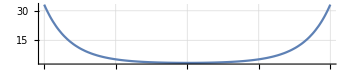

```mathematica
Plot[2.5+ Cosh[1.5 x]^4.,{x,-1,1},ImageSize->350,AspectRatio->0.2,GridLines->Automatic]
```

22--28. Nonlinear ODEs. Using a method of this section or separating variables, find the general solution. If an initial condition is given, find also the particular solution and sketch or graph it.
22. y' + y = y^2, y(0) = - 1/3

```mathematica
Clear["Global`*"]
```

```mathematica
eqn = y'[x]+y[x]==y[x]^2;
sol = DSolve[{eqn,y[0]==-1/3},y,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→Function[{x},-1/(-1+4 ⅇ^x)]}}

```mathematica
eqn/.sol//Simplify
```

{True}

```mathematica
y[0]/.sol[[1]]
```

-1/3

```mathematica
Clear["Global`*"]
```

23. y' + xy = xy^-1, y(0) = 3

```mathematica
eqn = y'[x]+x y[x]==x/y[x];
sol = DSolve[{eqn, y[0]==3},y,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{{y→Function[{x},√(ⅇ^(-x^2) (8+ⅇ^(x^2)))]}}

```mathematica
eqn/.sol//Simplify
```

{True}

```mathematica
y[0]/.sol[[1]]
```

3

```mathematica
solg = DSolve[{eqn},y,x]
```

{{y→Function[{x},-√(1+ⅇ^(-x^2+2 C[1]))]},{y→Function[{x},√(1+ⅇ^(-x^2+2 C[1]))]}}

The specific function is the teal-colored one.

```mathematica
Plot[{-√(1+ⅇ^(-x^2)),√(ⅇ^(-x^2) (8+ⅇ^(x^2)))},{x,-1,1},ImageSize->100,AspectRatio->Automatic]
```

-Graphics-

```mathematica
Clear["Global`*"]
```

24. y' + y = -x/y

```mathematica
eqn=y'[x]+y[x]==-x/y[x];
sol=DSolve[eqn,y,x]
```

{{y→Function[{x},-(√(1-2 x+2 ⅇ^(-2 x) C[1]))/(√2)]},{y→Function[{x},(√(1-2 x+2 ⅇ^(-2 x) C[1]))/(√2)]}}

```mathematica
eqn/.sol[[1]]//Simplify
```

True

```mathematica
eqn/.sol[[2]]//Simplify
```

True

```mathematica
Clear["Global`*"]
```

25. y' = 3.2y - 10 y^2

```mathematica
eqn=y'[x]==3.2 y[x]-10 y[x]^2;
sol = DSolve[eqn,y,x]
```

{{y→Function[{x},(8. 2.71828^(3.2 x))/(25. 2.71828^(3.2 x)+2.71828^(8. C[1]))]}}

```mathematica
eqn/.sol
```

{True}

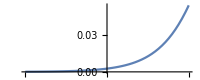

```mathematica
Plot[(8. 2.718281828459045^(3.2 x))/(25. 2.718281828459045^(3.2 x)+2.718281828459045^8.),{x,-1,1},ImageSize->200,AspectRatio->0.4]
```

```mathematica
Clear["Global`*"]
```

26. y' = (tan y)/(x - 1), y(0) = 1/2 π

```mathematica
eqn=y'[x]==Tan[y[x]]/(x-1);
sol=DSolve[{eqn,y[0]==π/2},y,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→Function[{x},ArcSin[1-x]]}}

```mathematica
eqn/.sol//Simplify
```

{True}

```mathematica
Clear["Global`*"]
```

27. y' = 1/(6 ⅇ^y - 2x)

```mathematica
eqn = y'[x]==1/(6 ⅇ^y[x]-2 x);
sol = DSolve[eqn,y,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→Function[{x},Log[1/6 (x+x^2/((x^3-54 C[1]+6 √3 √(-x^3 C[1]+27 C[1]^2))^(1/3))+(x^3-54 C[1]+6 √3 √(-x^3 C[1]+27 C[1]^2))^(1/3))]]},{y→Function[{x},Log[x/6-((1+ⅈ √3) x^2)/(12 (x^3-54 C[1]+6 √3 √(-x^3 C[1]+27 C[1]^2))^(1/3))-1/12 (1-ⅈ √3) (x^3-54 C[1]+6 √3 √(-x^3 C[1]+27 C[1]^2))^(1/3)]]},{y→Function[{x},Log[x/6-((1-ⅈ √3) x^2)/(12 (x^3-54 C[1]+6 √3 √(-x^3 C[1]+27 C[1]^2))^(1/3))-1/12 (1+ⅈ √3) (x^3-54 C[1]+6 √3 √(-x^3 C[1]+27 C[1]^2))^(1/3)]]}}

These odd-looking solutions seem able to check out when tested.

```mathematica
eqn/.sol[[1]]//Simplify
```

True

```mathematica
eqn/.sol[[2]]//Simplify
```

True

```mathematica
eqn/.sol[[3]]//Simplify
```

True

The following evaluation of sol[[1]] shows that the imaginary axis is an important component of this solution function.

```mathematica
N[Log[1/6 (x+x^2/((x^3-54 +6 √3 √(-x^3 +27))^(1/3))+(x^3-54 +6 √3 √(-x^3 +27))^(1/3))]/.x->1]
```

-0.136765-0.845369 ⅈ

So if I want to plot the function, I have to make room for the imaginary part. I assume that sol[[2]] and sol[[3]] also do a significant part of their business in the imaginary realm, but I’ll just stick with sol[[1]] for now.

```mathematica
d2=DiscretizeRegion@ImplicitRegion[-5≤x<5∧-5<y<5,{x,y}];
ParametricPlot[ReIm[Log[1/6 (x+x^2/((x^3-54 +6 √3 √(-x^3 +27))^(1/3))+(x^3-54 +6 √3 √(-x^3 +27))^(1/3))]],{x,y}∈d2,PlotRange->{{-2,2},{-2,1}},Frame->True,ImageSize->200,AspectRatio->Automatic]
```

-Graphics-

```mathematica
Clear["Global`*"]
```

28. 2xyy' + (x - 1)y^2 = x^2 ⅇ^x, (Set y^2 = z)

```mathematica
eqn = 2 x y[x] y'[x]+(x-1) y[x]^2==x^2 ⅇ^x;
sol = DSolve[eqn,y,x]
```

{{y→Function[{x},-(ⅇ^(-x/2) √x √(ⅇ^(2 x)+2 C[1]))/(√2)]},{y→Function[{x},(ⅇ^(-x/2) √x √(ⅇ^(2 x)+2 C[1]))/(√2)]}}

```mathematica
eqn/.sol[[1]]//Simplify
```

True

```mathematica
eqn/.sol[[2]]//Simplify
```

True

31 - 40 Modeling. Further applications

31. Newton’s law of cooling. If the temperature of a cake is 300℉ when it leaves the oven and is 200℉ ten minutes later, when will it be practically equal to the room temperature of 60℉, say when will it be 61℉?

From online sources such as http://vlab.amrita.edu/?sub=1&brch=194&sim=354&cnt=1 I can put it down as

```mathematica
200==60+(240)ⅇ^(-k t)
```

and

```mathematica
140==(240)ⅇ^(-k t)
```

```mathematica
Solve[140==(240)ⅇ^(-10k),k]
```

{{k→ConditionalExpression[1/10 (2 ⅈ π C[1]+Log[12/7]),C[1]∈Integers]}}

Discarding the imaginary part I retain

```mathematica
N[-1/10 Log[12/7]]
```

-0.0538997

as the value of k, in agreement with the text answer. (The minus sign was always part of k, the 10 factor merely occupying the space in between. Or, I could say that k will always be negative for things cooling down.)

When I re-insert k to calculate a specific case, the sign flips

```mathematica
Solve[239==ⅇ^(0.0538997t),t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→101.605}}

The text answer is given as 102 minutes, thus agreement to 3S.

33. Drug injection. Find and solve the model for drug injection into the bloodstream if, beginning at t = 0, a constant amount A g/min is injected and the drug is simultaneously removed at a rate proportional to the amount of the drug present at time t.

This looks like example 3 on p. 30, except that the input volume is constant instead of being based on a sinusoidal curve.

```mathematica
Clear["Global`*"]
```

y[t] is the amount of drug in the system at a given time t. The k y[t] is the proportional removal of the drug, aa the amount injected.

```mathematica
eqn=y'[t]-aa+k y[t]==0
```

-aa+k y[t]+y'[t]==0

```mathematica
sol=DSolve[{eqn,y[0]==0},y,t]
```

{{y→Function[{t},(aa ⅇ^(-k t) (-1+ⅇ^(k t)))/k]}}

```mathematica
eqn/.sol//Simplify
```

{True}

A specific amount of drug is injected, and continues to enter at a constant rate. The removal is proportional to the concentration, and the concentration gradually equilibrates.

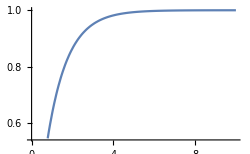

```mathematica
Plot[(aa ⅇ^(-k t) (-1+ⅇ^(k t)))/k/.{aa->1,k->1},{t,0,10},ImageSize->250]
```

35. Lake Erie. Lake Erie has a water volume of about 450 km^3 and a flow rate (in and out) of about 175 km^2 per year. If at some instant the lake has pollution concentration p = 0.04%, how long, approximately, will it take to decrease it to p/2, assuming that the inflow is much cleaner, say, it has pollution concentration p/4, and the mixture is uniform (an assumption that is only imperfectly true)? First guess.

This problem looks like a variation of the brine mixing problem described in example 5 on p. 14. y[t] will equal the amount of pollution product in the lake at any given time t. y'[t] = pollution inflow rate - pollution outflow rate. The pollution inflow rate is 0.0001*175 km^2 . The pollution outflow rate is not simply 0.0004*175 km^2 , because the assumption of mixing affects it. Since y[t] equals the amount of pollution product in the lake at any given time, 175/450 y[t] will describe the quantity which exits during a year. So the way to write the change in quantity of the item of interest, pollution, would be

```mathematica
Clear["Global`*"]
```

```mathematica
eqn=y'[t]==175.(0.0001-1/450. y[t])
```

y'[t]==175. (0.0001-0.00222222 y[t])

And the setup for calculating the governing equation, including the initial value, would be

```mathematica
sol=DSolve[{eqn,y[0]==0.0004*450.},y,t]
```

{{y→Function[{t},0.045 ⅇ^(-0.388889 t) (3.+1. ⅇ^(0.388889 t))]}}

For some reason it is necessary to chop off a bit to check the solution.

```mathematica
Chop[eqn/.sol//Simplify,10^-16]
```

{True}

Having got the formula for y[t], I can use Solve to determine the time required to reach the desired level of concentration of pollution

```mathematica
Solve[0.04500000000000001 ⅇ^(-0.38888888888888895 t) (2.9999999999999996+1. ⅇ^(0.38888888888888895 t))==0.0002,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→2.83646+8.07838 ⅈ}}

The answer is close the the text answer, which is 2.82 years. The imaginary, I believe, can be ignored.

36. Harvesting renewable resources. Fishing. Suppose that the population y[t] of a certain kind of fish is given by the logistic equation (11), p. 32, and fish are caught at a rate Hy proportional to y. Solve this so-called Schaefer model. Find the equilibrium solutions y_1 and y_2 (>0) when H < A. The expression y = Hy_2 is called the equilibrium harvest or sustainable yield corresponding to H. Why?

37. Harvesting. In problem 36 find and graph the solution satisfying y(0) = 2 when (for simplicity) A = B = 1 and H = 0.2. What is the limit? What does it mean? What if there were no fishing?

Numbered line (11) is
y'[t]=A y[t]-B y[t]^2

The text provides the solution to the equation as
y[t]=1/(c ⅇ^(-A t)+B/A)

But some disagreement with the text answer causes me to back up here and put down the ODE simply as

```mathematica
eqn=y'[t]==y[t]-y[t]^2
```

y'[t]==y[t]-y[t]^2

which is basic. Then adding in the initial value I call DSolve and get a solution

```mathematica
sol=DSolve[{eqn,y[0]==2},y,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→Function[{t},(2 ⅇ^t)/(-1+2 ⅇ^t)]}}

which I can test

```mathematica
eqn/.sol//Simplify
```

{True}

As for the solution which the text answer came up with,

```mathematica
PossibleZeroQ[(2 ⅇ^t)/(-1+2 ⅇ^t)-1/(1.25-0.75 ⅇ^(-0.8 t))]
```

False

However, they both meet the requirement of the initial value

```mathematica
(2 ⅇ^t)/(-1+2 ⅇ^t)/.t->0
```

2

```mathematica
1/(1.25-0.75 ⅇ^(-0.8 t))/.t->0
```

2.

But however I am sticking with mine.

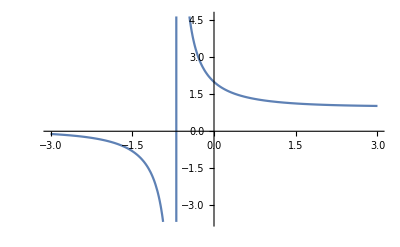

```mathematica
Plot[(2 ⅇ^t)/(-1+2 ⅇ^t),{t,-3,3}]
```

```mathematica
Limit[(2 ⅇ^t)/(-1+2 ⅇ^t),{t->∞}]
```

{1}

I am not really on topic here, since the text is talking about the logistics equation. Tossing out  a rough reference to that idea, I use material from Weisstein’s World, where r is the Malthusian parameter (rate of maximum population growth) .

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

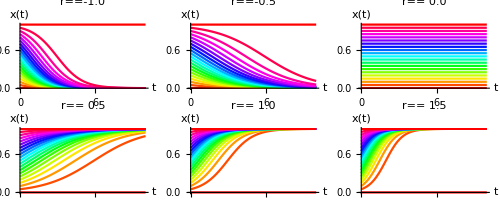

```mathematica
Show[GraphicsArray[Partition[Table[
Plot[Evaluate[Table[x0/(x0+ⅇ^(-r t)(1-x0)),{x0,0,1,.05}]],{t,0,10},
DisplayFunction->Identity,
PlotLabel->TraditionalForm[HoldForm[r]==PaddedForm[r,{2,1}]],
AxesLabel->TraditionalForm/@{t,x[t]},PlotStyle->Hue/@Range[0,1,.05],PlotRange->All],
{r,-1,1.5,.5}],3]
],ImageSize->500,GraphicsSpacing->{-.07,.1}]
```

39. Extinction vs. unlimited growth. If in a population y(t) the death rate is proportional to the population, and the birth rate is proportional to the chance encounters of meeting mates for reproduction, what will the model be? Without solving, find out what will eventually happen to a small initial population. To a large one. Then solve the model.

All I’m going to do for this one is to show the interesting demonstration by Abby Brown on the Wolfram Demonstration Project. As noted above, r is the rate of maximum population growth, K is the carrying capacity. P_0 is the starting population, and t is the elapsed time.

```mathematica
Manipulate[
Module[{pop,x,y,z},
If[p0==0,pop[t_]:=0,
pop[t_]:=KK/(((KK-p0)/p0)E^(-k t)+1)
];

Grid[{{
Show[

VectorPlot[{1,k y(1-y/KK)},{x,0,100},{y,0,1500},VectorStyle->{{Black,Arrowheads[0]}},VectorPoints->{21,31},VectorScale->0.04,

AspectRatio->1,Frame->False,Axes->True,AxesOrigin->{0,0},PlotRange->{{0,100},{0,1500}},

Ticks->{Join[Table[{n,Style[n,12,Black]},{n,0,100,10}],Table[{n+10,""},{n,-5,100,5}]],Join[Table[{n,Style[n,12,Black]},{n,0,1500,100}],Table[{n+50,""},{n,0,1500,100}]]},

AxesLabel->{Style["t",14,Black],Style["P",FontSize->14,Black]},ImageSize->325],

Plot[pop[t],{t,0,100},PlotStyle->Black],

Graphics[{
{Red,Line[{{t,0},{t,pop[t]}}]},
{Red,Line[{{0,pop[t]},{t,pop[t]}}]}
}]
],

Column[{"",
Graphics[{
{Lighter[Red,0.4],PointSize[0.025],Point[ptlist[[1;;Round@pop[t]]]]},
{Black,Opacity[0.5],Text[Style[ToString[Round@pop[t]],
Which[0<pop[t]<1000,150,pop[t]<10000,100,pop[t]<100000,80,pop[t]<10000000,62,pop[t]<20000000,55],
FontFamily->"Arial"],{0,0}]}
},PlotRange->10,ImageSize->275,PlotRangePadding->0.3],
Style[Row[{"          ",Checkbox[Dynamic[showexact]],Row[{" exact ",Text@Style["P",Italic],"  "}],If[showexact,NumberForm[pop[t],{20,5}]]}],"Label"]
}]}

}]
],
Row[{
Column[{
Control@{{p0,100,Subscript[Style["P",Italic],0]},0,500,1,Appearance->"Labeled"},
Control@{{k,0.08,Style["r",Italic]},0.03,0.2,Appearance->"Labeled"},
Control@{{KK,1000,Style["K",Italic]},10,1500,Appearance->"Labeled"},
Control@{{t,0,Style["t",Italic]},0,100,1,AnimationRate->2,Appearance->{"Labeled","Open"}}
}],
Column[{
Style[Row[{Style[" dP/dt",24],Style[" = ",Plain],"r P(",Style[1,Plain],"-P/K)"}],20,Italic,FontFamily->"Times"],
Style[Row[{Style["P(t)",20],Style[" = ",Plain,20],("K")/Row[{"A",e^(Style["-r t",14]),Style[" + 1",Plain]}],Style[" , A",20],Style[" = ",Plain,20],"(K -  SubscriptBox[P, 0])/P_0"}],24,Italic,FontFamily->"Times"],"",
"Play the animation for consistent time steps."
}]
}],
{{showexact,False,"show exact P"},{True,False},None},
TrackedSymbols:>{p0,k, KK,t  },
Initialization:>{ptlist=RandomReal[{-10,10},{10000,2}];}
]
```